```mathematica
(*
Выполнил ст.гр.221703
Воложинец А.А.
Вариант 3
*)
```

```mathematica
(*Задание 1*)
```

```mathematica
dy[x_, y_] := 0.3x*y+y^2;
Subscript[x, 0] = 0; Subscript[y, 0] = 0;
a = 0; b = 1;
```

```mathematica
(*
1.а
h = 0.1
*)
```

```mathematica
h = 0.1;
n = (b-a)/h;
(*Находим предикатор*)
predicator1 = {{Subscript[x, 0], Subscript[y, 0]}};
For[i = 1, i <= n, i++, AppendTo[predicator1, {Subscript[x, 0]+h*i,predicator1[[i, 2]]+h*dy[Subscript[x, 0]+h*(i-1), predicator1[[i, 2]]]}]];
predicator1
```

{{0,0},{0.1,0.},{0.2,0.},{0.3,0.},{0.4,0.},{0.5,0.},{0.6,0.},{0.7,0.},{0.8,0.},{0.9,0.},{1.,0.}}

```mathematica
(*Находим корректор*)
corrector1 = {{Subscript[x, 0], Subscript[y, 0]}};
For[i = 1, i <= n, i++, AppendTo[corrector1, {Subscript[x, 0]+i*h, corrector1[[i, 2]]+h/2(dy[Subscript[x, 0]+h*(i-1), corrector1[[i, 2]]]+dy[Subscript[x, 0]+h*i, predicator1[[i+1, 2]]])}]];
corrector1
```

{{0,0},{0.1,0.},{0.2,0.},{0.3,0.},{0.4,0.},{0.5,0.},{0.6,0.},{0.7,0.},{0.8,0.},{0.9,0.},{1.,0.}}

```mathematica
(*h=0.05*)
```

```mathematica
h = 0.05;
n = (b-a)/h;
(*Находим предикатор*)
predicator2 = {{Subscript[x, 0], Subscript[y, 0]}};
For[i = 1, i <= n, i++, AppendTo[predicator2, {Subscript[x, 0]+h*i,predicator2[[i, 2]]+h*dy[Subscript[x, 0]+h*(i-1), predicator2[[i, 2]]]}]];
predicator2
```

{{0,0},{0.05,0.},{0.1,0.},{0.15,0.},{0.2,0.},{0.25,0.},{0.3,0.},{0.35,0.},{0.4,0.},{0.45,0.},{0.5,0.},{0.55,0.},{0.6,0.},{0.65,0.},{0.7,0.},{0.75,0.},{0.8,0.},{0.85,0.},{0.9,0.},{0.95,0.},{1.,0.}}

```mathematica
(*Находим корректор*)
corrector2 = {{Subscript[x, 0], Subscript[y, 0]}};
For[i = 1, i <= n, i++, AppendTo[corrector2, {Subscript[x, 0]+i*h, corrector2[[i, 2]]+h/2(dy[Subscript[x, 0]+h*(i-1), corrector2[[i, 2]]]+dy[Subscript[x, 0]+h*i, predicator2[[i+1, 2]]])}]];
corrector2
```

{{0,0},{0.05,0.},{0.1,0.},{0.15,0.},{0.2,0.},{0.25,0.},{0.3,0.},{0.35,0.},{0.4,0.},{0.45,0.},{0.5,0.},{0.55,0.},{0.6,0.},{0.65,0.},{0.7,0.},{0.75,0.},{0.8,0.},{0.85,0.},{0.9,0.},{0.95,0.},{1.,0.}}

```mathematica
(*
1.б
h=0.1
*)
```

```mathematica
h = 0.1;
runge1 = {{Subscript[x, 0], Subscript[y, 0]}};
n = (b-a)/h;
Subscript[k, 1][x_, y_] := h*dy[x,y];
Subscript[k, 2][x_, y_] := h*dy[x+h/2,y+(Subscript[k, 1][x,y])/2];
Subscript[k, 3][x_, y_] := h*dy[x+h/2,y+(Subscript[k, 2][x,y])/2];
Subscript[k, 4][x_, y_] := h*dy[x+h,y+Subscript[k, 3][x,y]];
For[i = 1, i <= n, i++,
AppendTo[runge1, {Subscript[x, 0] + i*h,runge1[[i, 2]]+1/6(Subscript[k, 1][Subscript[x, 0]+h*(i-1), runge1[[i, 2]]] +2*Subscript[k, 2][Subscript[x, 0]+h*(i-1), runge1[[i, 2]]]+Subscript[k, 3][Subscript[x, 0]+h*(i-1), runge1[[i, 2]]]+Subscript[k, 4][Subscript[x, 0]+h*(i-1), runge1[[i, 2]]])}]];
runge1
```

{{0,0},{0.1,0.},{0.2,0.},{0.3,0.},{0.4,0.},{0.5,0.},{0.6,0.},{0.7,0.},{0.8,0.},{0.9,0.},{1.,0.}}

```mathematica
(*h=0.05*)
h = 0.05;
runge2 = {{Subscript[x, 0], Subscript[y, 0]}};
n = (b-a)/h;
Subscript[k, 1][x_, y_] := h*dy[x,y];
Subscript[k, 2][x_, y_] := h*dy[x+h/2,y+(Subscript[k, 1][x,y])/2];
Subscript[k, 3][x_, y_] := h*dy[x+h/2,y+(Subscript[k, 2][x,y])/2];
Subscript[k, 4][x_, y_] := h*dy[x+h,y+Subscript[k, 3][x,y]];
For[i = 1, i <= n, i++,
AppendTo[runge2, {Subscript[x, 0] + i*h,runge2[[i, 2]]+1/6(Subscript[k, 1][Subscript[x, 0]+h*(i-1), runge2[[i, 2]]] +2*Subscript[k, 2][Subscript[x, 0]+h*(i-1), runge2[[i, 2]]]+Subscript[k, 3][Subscript[x, 0]+h*(i-1), runge2[[i, 2]]]+Subscript[k, 4][Subscript[x, 0]+h*(i-1), runge2[[i, 2]]])}]];
runge2
```

{{0,0},{0.05,0.},{0.1,0.},{0.15,0.},{0.2,0.},{0.25,0.},{0.3,0.},{0.35,0.},{0.4,0.},{0.45,0.},{0.5,0.},{0.55,0.},{0.6,0.},{0.65,0.},{0.7,0.},{0.75,0.},{0.8,0.},{0.85,0.},{0.9,0.},{0.95,0.},{1.,0.}}

```mathematica
(*1.в*)
```

```mathematica
Clear[x, y];
dsolve = DSolve[{y'[x] == 0.3x*y[x]+y[x]^2, y[Subscript[x, 0]] == Subscript[y, 0]}, y[x], x]
ndsolve = NDSolve[{y'[x]==dy[x,y[x]],y[Subscript[x, 0]]==Subscript[y, 0]},y[x],{x,0,1}]
```

{{y[x]→0}}

{{y[x]→InterpolatingFunction[…][x]}}

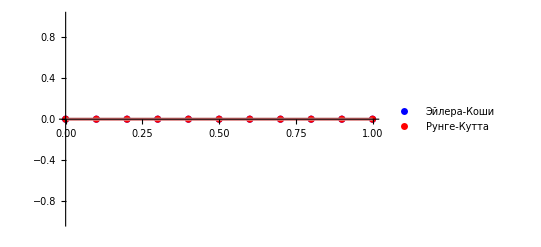

```mathematica
(*методы Эйлера-Коши и Рунге-Кутта с шагом 0.1*)
eulerGraph = ListPlot[corrector1, PlotStyle-> Blue, PlotLegends -> PointLegend[{Blue}, {"Эйлера-Коши"}]];
rungeGraph = ListPlot[runge1, PlotStyle -> Red, PlotLegends -> PointLegend[{Red},{"Рунге-Кутта"}] ];
ndsolveGraph=Plot[Evaluate[y[x]/.ndsolve],{x,0,1},ImageSize->Small, PlotStyle->Gray, PlotLegends -> {"NDSolve"}];
dsolveGraph=Plot[Evaluate[y[x]/.dsolve],{x,0,1},ImageSize->Small, PlotStyle->Pink, PlotLegends -> {"DSolve"}];
Show[eulerGraph, rungeGraph, ndsolveGraph, dsolveGraph]
```

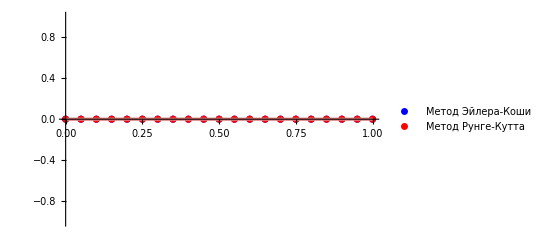

```mathematica
(*Методы Эйлера-Коши и Рунге-Кутта с шагом 0.05*)
eulerGraph = ListPlot[corrector2, PlotStyle-> Blue, PlotLegends -> PointLegend[{Blue}, {"Метод Эйлера-Коши"}]];
rungeGraph = ListPlot[runge2, PlotStyle -> Red, PlotLegends -> PointLegend[{Red},{"Метод Рунге-Кутта"}] ];
ndsolveGraph=Plot[Evaluate[y[x]/.ndsolve],{x,0,1},ImageSize->Small, PlotStyle->Gray, PlotLegends -> {"NDSolve"}];
dsolveGraph=Plot[Evaluate[y[x]/.dsolve],{x,0,1},ImageSize->Small, PlotStyle->Pink, PlotLegends -> {"DSolve"}];
Show[eulerGraph, rungeGraph, ndsolveGraph, dsolveGraph]
```

```mathematica
(*Вывод: исходя из графиков, можно увидеть что методы накладываются друг на друга и сказать, что точнее не удается.*)
```

```mathematica
(*Задание 2*)
```

```mathematica
dy[x_, y_, z_] := 2y+z+3 ⅇ^-x; Subscript[y, 0] = 1; Subscript[x, 0] = 0;
dz[x_, y_, z_] := y-2z+4 ⅇ^x; Subscript[z, 0] = 2;
a = 0; b = 1;
```

```mathematica
(*
2.a
h = 0.1
*)
```

```mathematica
h = 0.1;
n = (b-a)/h;
eulerY1 = {{Subscript[x, 0], Subscript[y, 0]}};
eulerZ1 = {{Subscript[x, 0],Subscript[z, 0]}};
For[i = 1, i <= n, i++, AppendTo[eulerY1, {Subscript[x, 0]+h*i,eulerY1[[i, 2]]+h*dy[Subscript[x, 0]+h*(i-1), eulerY1[[i, 2]], eulerZ1[[i, 2]]]}];AppendTo[eulerZ1, {Subscript[x, 0]+h*i,eulerZ1[[i, 2]]+h*dz[Subscript[x, 0]+h*i, eulerY1[[i, 2]], eulerZ1[[i, 2]]]}]]
eulerY1
eulerZ1
```

{{0,1},{0.1,1.7},{0.2,2.52566},{0.3,3.51363},{0.4,4.70763},{0.5,6.16028},{0.6,7.93535},{0.7,10.1104},{0.8,12.78},{0.9,16.0598},{1.,20.0911}}

{{0,2},{0.1,2.14207},{0.2,2.37222},{0.3,2.69028},{0.4,3.10032},{0.5,3.61051},{0.6,4.23328},{0.7,4.98566},{0.8,5.88978},{0.9,6.97367},{1.,8.27223}}

```mathematica
(*h = 0.05*)
```

```mathematica
h = 0.05;
n = (b-a)/h;
eulerY2 = {{Subscript[x, 0], Subscript[y, 0]}};
eulerZ2 = {{Subscript[x, 0],Subscript[z, 0]}};
For[i = 1, i <= n, i++, AppendTo[eulerY2, {Subscript[x, 0]+h*i,eulerY2[[i, 2]]+h*dy[Subscript[x, 0]+h*(i-1), eulerY2[[i, 2]], eulerZ2[[i, 2]]]}];AppendTo[eulerZ2, {Subscript[x, 0]+h*i,eulerZ2[[i, 2]]+h*dz[Subscript[x, 0]+h*i, eulerY2[[i, 2]], eulerZ2[[i, 2]]]}]]
eulerY2
eulerZ2
```

{{0,1},{0.05,1.35},{0.1,1.7307},{0.15,2.14663},{0.2,2.60277},{0.25,3.10457},{0.3,3.65803},{0.35,4.26979},{0.4,4.94716},{0.45,5.69823},{0.5,6.53197},{0.55,7.45833},{0.6,8.48833},{0.65,9.63422},{0.7,10.9096},{0.75,12.3295},{0.8,13.9108},{0.85,15.6721},{0.9,17.6342},{0.95,19.82},{1.,22.2552}}

{{0,2},{0.05,2.06025},{0.1,2.14276},{0.15,2.24739},{0.2,2.37426},{0.25,2.52378},{0.3,2.6966},{0.35,2.89366},{0.4,3.11615},{0.45,3.36555},{0.5,3.64365},{0.55,3.95254},{0.6,4.29462},{0.65,4.67268},{0.7,5.08988},{0.75,5.54977},{0.8,6.05638},{0.85,6.61421},{0.9,7.22831},{0.95,7.90433},{1.,8.64855}}

```mathematica
(*
2.б
h = 0.1
*)
```

```mathematica
h = 0.1;
n = (b-a)/h;
rungeY1 = {{Subscript[x, 0], Subscript[y, 0]}};
rungeZ1 = {{Subscript[x, 0], Subscript[z, 0]}};
Subscript[k, 1][x_, y_, z_] := h*dy[x,y,z];
Subscript[r, 1][x_, y_, z_] :=h*dz[x, y,z];
Subscript[k, 2][x_, y_, z_] := h*dy[x+h/2,y+(Subscript[k, 1][x, y, z])/2,z+(Subscript[r, 1][x,y, z])/2];
Subscript[r, 2][x_, y_, z_] := h*dz[x + h/2,y+(Subscript[k, 1][x, y, z])/2,z+(Subscript[r, 1][x, y, z])/2];
Subscript[k, 3][x_, y_, z_] := h*dy[x+h/2,y+(Subscript[k, 2][x,y, z])/2, z+(Subscript[r, 2][x,y, z])/2];
Subscript[r, 3][x_, y_, z_] := h*dz[x + h/2,y+(Subscript[k, 2][x, y, z])/2,z+(Subscript[r, 2][x, y, z])/2];
Subscript[k, 4][x_, y_, z_] := h*dy[x+h,y+Subscript[k, 3][x,y,z], z+Subscript[r, 3][x, y, z]];
Subscript[r, 4][x_, y_, z_] := h*dz[x+h,y+Subscript[k, 3][x,y,z], z+Subscript[r, 3][x, y, z]];
```

```mathematica
For[i = 1, i <= n, i++,
AppendTo[rungeY1, {Subscript[x, 0] + i*h,rungeY1[[i, 2]]+1/6(Subscript[k, 1][Subscript[x, 0]+h*(i-1), rungeY1[[i, 2]], rungeZ1[[i, 2]]] +2*Subscript[k, 2][Subscript[x, 0]+h*(i-1), rungeY1[[i, 2]], rungeZ1[[i, 2]]]+2*Subscript[k, 3][Subscript[x, 0]+h*(i-1), rungeY1[[i, 2]], rungeZ1[[i, 2]]]+Subscript[k, 4][Subscript[x, 0]+h*(i-1), rungeY1[[i, 2]], rungeZ1[[i, 2]]])}];
AppendTo[rungeZ1, {Subscript[x, 0] + i*h,rungeZ1[[i, 2]]+1/6(Subscript[r, 1][Subscript[x, 0]+h*(i-1), rungeY1[[i, 2]], rungeZ1[[i, 2]]] +2*Subscript[r, 2][Subscript[x, 0]+h*(i-1), rungeY1[[i, 2]], rungeZ1[[i, 2]]]+2*Subscript[r, 3][Subscript[x, 0]+h*(i-1), rungeY1[[i, 2]], rungeZ1[[i, 2]]]+Subscript[r, 4][Subscript[x, 0]+h*(i-1), rungeY1[[i, 2]], rungeZ1[[i, 2]]])}]];
rungeY1
rungeZ1
```

{{0,1},{0.1,1.76628},{0.2,2.69295},{0.3,3.8286},{0.4,5.23308},{0.5,6.98047},{0.6,9.16289},{0.7,11.8951},{0.8,15.3205},{0.9,19.6182},{1.,25.0119}}

{{0,2},{0.1,2.14485},{0.2,2.38024},{0.3,2.71072},{0.4,3.14537},{0.5,3.69818},{0.6,4.38867},{0.7,5.24281},{0.8,6.29419},{0.9,7.58566},{1.,9.17138}}

```mathematica
(*h = 0.05*)
```

```mathematica
h = 0.05;
n = (b-a)/h;
rungeY2 = {{Subscript[x, 0], Subscript[y, 0]}};
rungeZ2 = {{Subscript[x, 0], Subscript[z, 0]}};
Subscript[k, 1][x_, y_, z_] := h*dy[x,y,z];
Subscript[r, 1][x_, y_, z_] :=h*dz[x, y,z];
Subscript[k, 2][x_, y_, z_] := h*dy[x+h/2,y+(Subscript[k, 1][x, y, z])/2,z+(Subscript[r, 1][x,y, z])/2];
Subscript[r, 2][x_, y_, z_] := h*dz[x + h/2,y+(Subscript[k, 1][x, y, z])/2,z+(Subscript[r, 1][x, y, z])/2];
Subscript[k, 3][x_, y_, z_] := h*dy[x+h/2,y+(Subscript[k, 2][x,y, z])/2, z+(Subscript[r, 2][x,y, z])/2];
Subscript[r, 3][x_, y_, z_] := h*dz[x + h/2,y+(Subscript[k, 2][x, y, z])/2,z+(Subscript[r, 2][x, y, z])/2];
Subscript[k, 4][x_, y_, z_] := h*dy[x+h,y+Subscript[k, 3][x,y,z], z+Subscript[r, 3][x, y, z]];
Subscript[r, 4][x_, y_, z_] := h*dz[x+h,y+Subscript[k, 3][x,y,z], z+Subscript[r, 3][x, y, z]];
```

```mathematica
For[i = 1, i <= n, i++,
AppendTo[rungeY2, {Subscript[x, 0] + i*h,rungeY2[[i, 2]]+1/6(Subscript[k, 1][Subscript[x, 0]+h*(i-1), rungeY2[[i, 2]], rungeZ2[[i, 2]]] +2*Subscript[k, 2][Subscript[x, 0]+h*(i-1), rungeY2[[i, 2]], rungeZ2[[i, 2]]]+2*Subscript[k, 3][Subscript[x, 0]+h*(i-1), rungeY2[[i, 2]], rungeZ2[[i, 2]]]+Subscript[k, 4][Subscript[x, 0]+h*(i-1), rungeY2[[i, 2]], rungeZ2[[i, 2]]])}];
AppendTo[rungeZ2, {Subscript[x, 0] + i*h,rungeZ2[[i, 2]]+1/6(Subscript[r, 1][Subscript[x, 0]+h*(i-1), rungeY2[[i, 2]], rungeZ2[[i, 2]]] +2*Subscript[r, 2][Subscript[x, 0]+h*(i-1), rungeY2[[i, 2]], rungeZ2[[i, 2]]]+2*Subscript[r, 3][Subscript[x, 0]+h*(i-1), rungeY2[[i, 2]], rungeZ2[[i, 2]]]+Subscript[r, 4][Subscript[x, 0]+h*(i-1), rungeY2[[i, 2]], rungeZ2[[i, 2]]])}]];
rungeY2
rungeZ2
```

{{0,1},{0.05,1.36577},{0.1,1.76629},{0.15,2.20678},{0.2,2.69298},{0.25,3.23125},{0.3,3.82866},{0.35,4.49306},{0.4,5.23318},{0.45,6.05875},{0.5,6.98062},{0.55,8.01091},{0.6,9.16312},{0.65,10.4524},{0.7,11.8955},{0.75,13.5114},{0.8,15.321},{0.85,17.3481},{0.9,19.6188},{0.95,22.1628},{1.,25.0128}}

{{0,2},{0.05,2.06122},{0.1,2.14485},{0.15,2.25105},{0.2,2.38024},{0.25,2.53314},{0.3,2.71072},{0.35,2.91428},{0.4,3.14538},{0.45,3.40594},{0.5,3.6982},{0.55,4.02479},{0.6,4.38871},{0.65,4.79343},{0.7,5.24287},{0.75,5.74148},{0.8,6.29429},{0.85,6.90694},{0.9,7.58581},{0.95,8.33802},{1.,9.17158}}

```mathematica
(*2.в*)
```

```mathematica
dsolveMethodY = DSolve[{y'[x] == dy[x, y[x], z[x]], z'[x] == dz[x, y[x], z[x]], y[Subscript[x, 0]] == Subscript[y, 0], z[Subscript[x, 0]] == Subscript[z, 0]}, {y, z}, x][[1]][[1]]
ndsolveMethodY = NDSolve[{y'[x] == dy[x, y[x], z[x]], z'[x] == dz[x, y[x], z[x]], y[Subscript[x, 0]] == Subscript[y, 0], z[Subscript[x, 0]] == Subscript[z, 0]}, {y, z}, {x, a, b}][[1]][[1]]
dsolveMethodZ = DSolve[{y'[x] == dy[x, y[x], z[x]], z'[x] == dz[x, y[x], z[x]], y[Subscript[x, 0]] == Subscript[y, 0], z[Subscript[x, 0]] == Subscript[z, 0]}, {y, z}, x][[1]][[2]]
ndsolveMethodZ = NDSolve[{y'[x] == dy[x, y[x], z[x]], z'[x] == dz[x, y[x], z[x]], y[Subscript[x, 0]] == Subscript[y, 0], z[Subscript[x, 0]] == Subscript[z, 0]}, {y, z}, {x, a, b}][[1]][[2]]
```

y→Function[{x},1/8 ⅇ^(-x-√5 x) (7 ⅇ^x-5 √5 ⅇ^x-6 ⅇ^(√5 x)+7 ⅇ^(x+2 √5 x)+5 √5 ⅇ^(x+2 √5 x))]

y→InterpolatingFunction[…]

z→Function[{x},-1/8 ⅇ^(-x-√5 x) (-11 ⅇ^x-3 √5 ⅇ^x+6 ⅇ^(√5 x)-11 ⅇ^(x+2 √5 x)+3 √5 ⅇ^(x+2 √5 x))]

z→InterpolatingFunction[…]

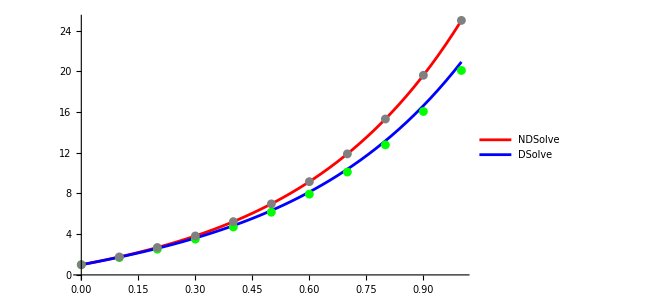

```mathematica
(*Функция y, шаг 0.1*)
ndsolveMethodYGraph=Plot[Evaluate[y[x]/.ndsolveMethodY],{x,0,1},ImageSize->Small, PlotStyle->Red, PlotLegends->{"NDSolve"}];
dsolveMethodYGraph=Plot[Evaluate[y[x]/.dsolveMethodY],{x,0,1},ImageSize->Small, PlotStyle->Blue, PlotLegends->{"DSolve"}];
eulerMethodYGraph = ListPlot[eulerY1, PlotStyle -> Green, PlotLegends -> PointLegend[{Green}, {"Метод Эйлера"}]];
rungeMethodYGraph = ListPlot[rungeY1, PlotStyle -> Gray, PlotLegends -> PointLegend[{Gray}, {"Метод Рунге-Кутта"}]];
Show[ndsolveMethodYGraph, dsolveMethodYGraph, eulerMethodYGraph, rungeMethodYGraph]
```

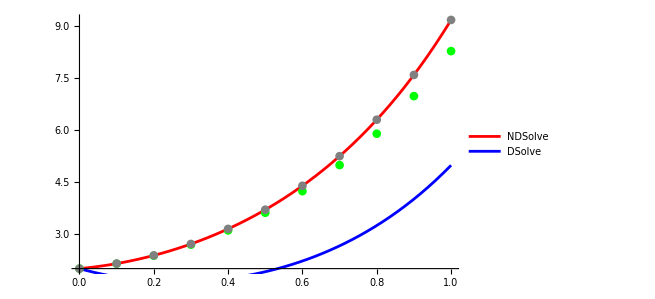

```mathematica
(*Функция z, шаг 0.1*)
ndsolveMethodZGraph=Plot[Evaluate[z[x]/.ndsolveMethodZ],{x,0,1},ImageSize->Small, PlotStyle->Red, PlotLegends->{"NDSolve"}];
dsolveMethodZGraph=Plot[Evaluate[z[x]/.dsolveMethodZ],{x,0,1},ImageSize->Small, PlotStyle->Blue, PlotLegends->{"DSolve"}];
eulerMethodZGraph = ListPlot[eulerZ1, PlotStyle -> Green, PlotLegends -> PointLegend[{Green}, {"Метод Эйлера"}]];
rungeMethodZGraph = ListPlot[rungeZ1, PlotStyle -> Gray, PlotLegends -> PointLegend[{Gray}, {"Метод Рунге-Кутта"}]];
Show[ndsolveMethodZGraph, dsolveMethodZGraph, eulerMethodZGraph, rungeMethodZGraph]
```

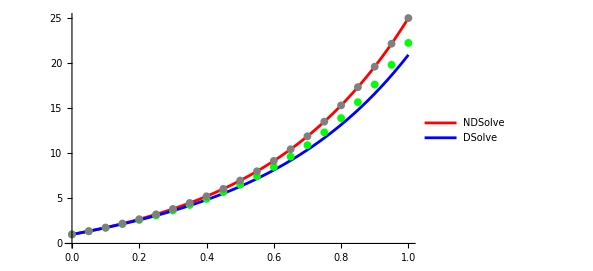

```mathematica
(*Функция y, шаг 0.05*)
ndsolveMethodYGraph=Plot[Evaluate[y[x]/.ndsolveMethodY],{x,0,1},ImageSize->Small, PlotStyle->Red, PlotLegends->{"NDSolve"}];
dsolveMethodYGraph=Plot[Evaluate[y[x]/.dsolveMethodY],{x,0,1},ImageSize->Small, PlotStyle->Blue, PlotLegends->{"DSolve"}];
eulerMethodYGraph = ListPlot[eulerY2, PlotStyle ->Green, PlotLegends -> PointLegend[{Green}, {"Метод Эйлера"}]];
rungeMethodYGraph = ListPlot[rungeY2, PlotStyle -> Gray, PlotLegends -> PointLegend[{Gray}, {"Метод Рунге-Кутта"}]];
Show[ndsolveMethodYGraph, dsolveMethodYGraph, eulerMethodYGraph, rungeMethodYGraph]
```

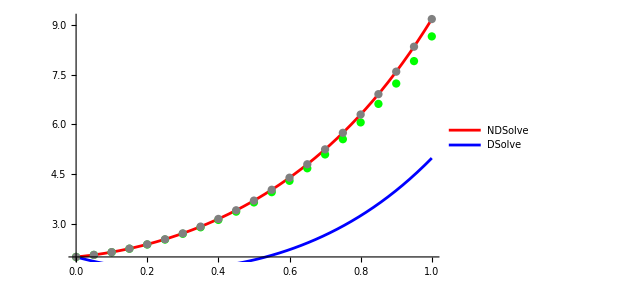

```mathematica
(*Функция z, шаг 0.05*)
ndsolveMethodZGraph=Plot[Evaluate[z[x]/.ndsolveMethodZ],{x,0,1},ImageSize->Small, PlotStyle->Red, PlotLegends->{"NDSolve"}];
dsolveMethodZGraph=Plot[Evaluate[z[x]/.dsolveMethodZ],{x,0,1},ImageSize->Small, PlotStyle->Blue, PlotLegends->{"DSolve"}];
eulerMethodZGraph = ListPlot[eulerZ2, PlotStyle -> Green, PlotLegends -> PointLegend[{Green}, {"Метод Эйлера"}]];
rungeMethodZGraph = ListPlot[rungeZ2, PlotStyle -> Gray, PlotLegends ->PointLegend[{Gray}, {"Метод Рунге-Кутта"}]];
Show[ndsolveMethodZGraph, dsolveMethodZGraph, eulerMethodZGraph, rungeMethodZGraph]
```

```mathematica
(*Вывод: основываясь на графиках, при шаге 0.05 результат получается более точным, также метод Рунге-Кутта оказался более точным*)
```